```mathematica
dir="D:\\newLight3"
```

D:\newLight3

```mathematica
dir=SystemDialogInput["Directory"]
```

D:\grafiliv - stayin alive 2\

```mathematica
GetParent[orgNo_]:=Module[{path,g,n,s,i},
Quiet[
path = StringForm["``\\organisms\\org``.json",dir,orgNo];
{g,n,s,i}=Import[path//ToString];
"parent"/.i
]
]
GetLivingOrganisms[frameNo_]:=Module[{path,file,headings,items,applyHeading,organisms},
path = StringForm["``\\output\\frame``.csv",dir,frameNo];
file=Import[path//ToString];
headings=file//First;
items=file//Rest;
applyHeading[item_]:=MapThread[#1-> #2&,{headings,item}];
items = applyHeading/@items;
organisms="o"/.items//DeleteDuplicates;
Select[organisms,#>=0&]
]
drawRelations[orgs_,steps_]:=Module[{g,gs},
gs=ParallelMap[
NestGraph[
If[#<0,-1,GetParent[#]]&,
#,steps
]&,
orgs
];
g=Parallelize[GraphUnion@@gs];
HighlightGraph[g,orgs,
(*VertexLabels->"Name"*)
GraphLayout->{"LayeredEmbedding","RootVertex"->Min[VertexList[g]]},
VertexLabels->Placed["Name",Tooltip]
]
]
stepsToLCA[a_,b_]:=Module[{lA={a},lB={b}},
While[ContainsNone[lA,lB],
AppendTo[lA,GetParent[Last[lA]]];
AppendTo[lB,GetParent[Last[lB]]];
];
Min[Length[lA],Length[lB]]-1
]
stepsToLCALessThan[a_,b_,max_]:=Monitor[Module[{lA={a},lB={b}},
While[ContainsNone[lA,lB],
If[Length[lA]≤ max &&Length[lB]≤ max ,Return[False]];
AppendTo[lA,GetParent[Last[lA]]];
AppendTo[lB,GetParent[Last[lB]]];
];
True
],lA]
stepsToLCALessThanNew[orgA_,orgB_,max_]:=Module[{a=orgA,b=orgB,stepsA=0, stepsB=0},
While[stepsA<max && stepsB<max,
If[a>b, a=GetParent[a];stepsA++,
If[a<b,b=GetParent[b];stepsB++,
(* Else a=b *) Return[True]];
];
];
False
]
```

```mathematica
step=1160000;
```

```mathematica
living=GetLivingOrganisms[step];
```

```mathematica
stepsToLCALessThan[633917,628974,100]//Timing
stepsToLCALessThanNew[633917,628974,100]//Timing
```

{0.,False}

{2.48438,False}

```mathematica
Length[living]
```

3880

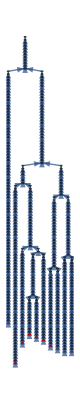

```mathematica
drawRelations[RandomChoice[living,10],100]
```

```mathematica
drawRelations[living,100]
```

$Aborted

```mathematica
stepsToLCALessThan[5,10,100]
stepsToLCA[5,10]
```

False

$Aborted

```mathematica
With[{pair=RandomChoice[living,2]},drawRelations[pair,stepsToLCA@@pair]]
```

$Aborted

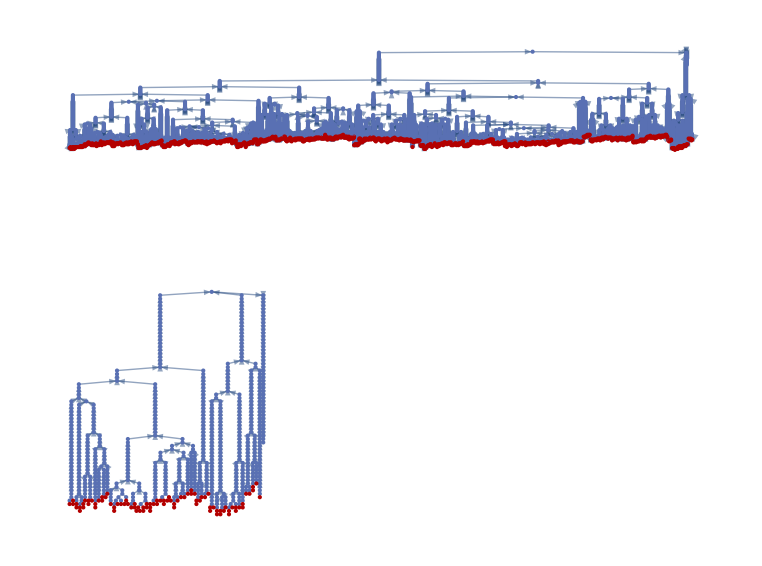

```mathematica
g=drawRelations[living,100]
```

```mathematica
gu=GraphUnion[drawRelations[{334014,334324},200],g];
```

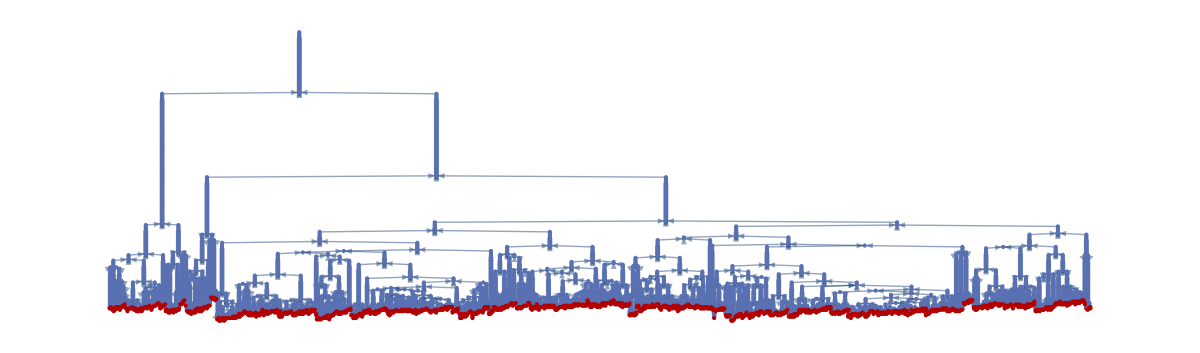

```mathematica
HighlightGraph[
gu,
living,
ImageSize->1200,
VertexLabels->Placed["Name",Tooltip],
GraphLayout->{
"LayeredEmbedding",
"RootVertex"->Min[VertexList[gu]]
}
,EdgeShapeFunction->"Line"
]
```

```mathematica
findSpecies[pool_]:=Module[{orgs = pool,definingSpecimen,s,sel,species,temp},
Reap[
While[Length[orgs]>0,
definingSpecimen=First[orgs];
sel=ParallelMap[
stepsToLCALessThanNew[#,definingSpecimen,50]&,
orgs
];
Sow[Pick[orgs,sel]];
orgs=Pick[orgs,sel,False];
Print[orgs//Length];
]
]
];
```

```mathematica
Take[living,10]
```

{633664,633330,633578,634163,634310,634562,634565,632584,634981,633933}

```mathematica
stepsToLCALessThanNew[633330,633578,50]
```

False

```mathematica
species=findSpecies[living]
```

3201

2777

1029

1006

816

735

618

573

533

461

388

383

329

285

246

116

113

92

69

61

46

44

33

23

17

10

0

{Null,{{{633664,634519,634496,634605,634082,634478,632412,634383,633980,632928,632544,632496,633417,634669,633801,632573,632956,634262,633634,633537,634244,628292,634387,634348,634078,634089,632058,633475,634032,632812,634298,632427,634381,634476,634746,631908,633846,633306,632811,634928,635041,634850,634378,634889,633103,634986,633652,634806,634558,632797,634863,634812,632599,634524,634947,633265,634592,633783,634140,632390,633228,631976,634358,633204,632805,632600,634690,631955,631907,633797,632625,632071,632332,633522,634775,634497,633979,632347,634744,634803,634756,632741,632482,632994,633490,632638,632690,632793,632159,632396,632172,633137,634650,633255,633446,632342,633986,633068,633978,634938,634503,633938,632662,634127,634694,632010,631953,634176,632930,632221,632973,634912,632423,634135,634513,632417,632817,634248,633461,632943,634291,634159,633834,634488,633193,633515,632859,633572,632254,634292,632971,634508,631959,634588,633547,633018,634579,634064,634612,633432,634040,632171,631957,633311,633077,634955,634455,634467,634543,634352,632628,633587,632934,633253,634968,632730,632321,633406,634123,633097,634504,633623,634716,633008,634189,633199,634749,632710,633619,633201,633669,633107,634510,634165,632976,634207,633733,632179,632491,634877,633216,633962,632261,635031,633244,634412,632936,632015,632647,634481,634312,634404,634886,634799,634633,632829,632549,632591,632767,633425,634862,632926,632369,633543,632881,632234,632939,632990,632180,634388,633112,632862,634870,632466,633672,633676,634983,633457,632959,633143,633214,633309,633388,634636,633912,633481,634212,632199,634944,628337,632405,634576,633653,632055,633260,634036,632518,632745,634086,634973,634360,633459,632476,634875,634023,634438,634776,633688,633007,632680,633721,632753,632800,628348,633573,634491,634297,634769,634541,634362,634667,633717,634607,632752,634632,633037,635047,632855,634984,634096,634894,633766,634551,633763,634530,635001,634989,635033,634046,633206,634993,634215,633678,634778,635012,634641,635015,633745,633751,633843,634526,633431,634871,632413,633221,634390,634022,634536,634961,635006,634447,633767,634341,633743,635063,632967,634656,634350,634395,633259,633536,633421,628381,633848,634522,633712,634837,632836,628391,634460,632898,634188,634787,634920,634540,633891,632819,632541,633568,634445,634347,634472,628403,632057,634017,634398,634591,633807,628415,634614,634191,634134,633034,632430,633609,632874,634437,632669,633188,634300,632853,635014,632448,632315,633410,633890,634369,628471,633058,633194,628475,628476,634940,632551,628487,632897,634921,634198,633276,633166,634884,632848,632833,633050,633153,628525,633274,632919,628560,632535,632748,628572,634321,628599,633366,634042,628604,632609,628610,634179,634572,634401,628666,628669,633800,634453,634405,628674,632548,632515,628684,634992,634752,634926,628736,634888,632562,633040,632521,633385,633073,632334,634195,635038,634305,634211,628802,632658,633076,633251,634258,634051,633774,628904,628123,628125,633770,628139,628161,634774,628944,628199,628952,628232,628963,628250,628253,628266,628274,634807,635044,628992,634259,629004,629017,633170,629042,629093,629108,629111,634847,629123,629128,629140,629142,629158,629178,629179,629205,629210,633451,629216,629224,629225,634153,629241,633864,634290,633356,629308,629322,629353,629381,633383,629391,629394,629395,629398,629425,629426,629445,629448,629461,629465,629472,629492,629499,634533,629572,629578,629588,629596,629598,632527,629618,629621,629633,629639,629656,629662,629695,629703,629737,629740,629753,633598,629774,629787,629788,629807,629823,629824,629835,629836,629837,634286,629845,629860,629888,629901,629912,629926,629941,629976,629978,629988,635020,630026,630041,630067,630072,630078,630095,630096,630125,630148,630152,630169,630177,630187,630204,630217,630248,630259,630261,630295,630296,630328,630347,630361,630377,630382,630383,630458,630459,630467,630469,630470,630486,630538,630542,630545,630572,630580,630615,630630,630639,630658,630675,630687,630713,630734,630737,630738,630743,630754,630761,630765,630770,630773,630789,630828,630840,630852,630874,630879,630886,630896,630902,630904,630905,630915,630921,630942,630948,630954,630986,631001,631012,631033,631034,631068,631079,631097,631111,631112,631114,631122,631128,631168,631179,631195,631206,631207,631208,631217,631244,631257,631265,631266,631269,631288,631310,631312,631317,631321,631323,631338,631340,631341,631349,631359,631361,631365,631378,631400,631405,631408,631414,631423,631430,631431,631443,631447,631449,631489,631492,631516,631522,631547,631555,631556,631563,631567,631580,631583,631584,631593,631613,631614,631628,631635,631637,631653,631655,631667,631702,631727,631739,631788,631793,631795,631797,631818,631832,631835,631845,631875,631884},{633330,634163,634689,634377,633827,632627,633452,634322,633825,634537,634418,634584,634227,634734,633017,634389,632333,633900,633135,633816,635022,634313,633358,634451,634793,634853,635005,633716,632445,634771,634845,633847,633699,632771,634620,632820,634201,632260,634097,632503,632550,633419,633512,633140,634495,634384,634703,634718,633416,632706,633486,633684,634996,633105,633386,632458,632050,633559,635048,632056,632176,634416,633640,632840,634905,634324,633184,633435,634441,632034,635029,634619,631994,633741,632237,634559,634070,634149,632498,632790,632229,634882,634190,632286,628317,634702,634117,633567,633689,632182,635019,632013,634763,632938,633220,633043,632882,633094,632834,633168,633854,633909,634110,634827,632081,633494,634477,634829,633650,633994,633837,634279,632581,634004,632394,633710,633342,633542,634739,633429,634811,634161,631926,634964,634007,634364,633226,633948,633945,634684,635007,634683,634028,632223,634972,632330,634896,628367,633286,632734,634998,634516,634323,634047,628394,632317,634059,633232,635030,633691,633133,633974,634269,632325,632736,632005,628420,633145,632486,632948,634501,633937,628443,632709,633739,633211,633088,632270,631911,632449,632492,633635,632353,633258,628494,634901,632256,633651,633503,632743,628532,632370,633373,633124,634903,632792,633002,628587,628589,632694,633038,633004,633561,628603,628612,633661,632999,628646,634648,632852,628679,634598,628688,628689,632185,632991,634654,634083,628773,634712,628786,632594,634649,635054,632679,632470,628813,632178,633322,632768,628876,628888,632893,632963,628908,628909,633217,628916,628917,628119,634316,632406,632666,632630,628953,628958,628233,628252,628269,628283,628979,633171,628989,629031,629038,629040,629041,629047,629065,629079,629082,634647,629126,629141,629145,633465,629191,629253,629271,629287,629310,633756,629375,629387,629393,629403,634969,629446,629523,629545,634808,629558,629571,629574,629622,629630,629635,633636,629644,629648,634581,634256,629670,629675,629681,629692,629731,629763,629771,629793,629810,634956,629826,629830,629853,629872,634731,629934,629945,629950,629993,632632,633039,630092,630113,630114,630117,630135,630138,630142,630174,630176,632941,630243,630258,630290,634761,630303,630337,630352,630357,630359,630365,630366,630397,630401,630405,630480,630496,630509,634317,630521,630552,630562,630570,634375,630592,630601,630618,630629,630643,630648,630670,630693,630703,630708,630747,630752,630783,630786,630790,630795,630799,630808,630825,630910,630920,630936,630958,630978,630994,630995,631007,631010,631030,631057,631075,631092,631127,631137,631171,631185,631186,631188,631203,631223,631238,631239,631250,631254,631290,631302,631316,631319,631326,631330,631332,631333,631360,631413,631420,631474,631475,631488,631499,631502,631515,631527,631588,631599,631603,631605,631616,631618,631623,631660,631674,631689,631690,631706,631707,631708,631719,631722,631731,631736,631755,631768,631771,631782,631794,631826,631852,631882},{633578,634310,634562,634565,632584,634981,633933,634594,633903,634783,634470,634770,633897,633869,634223,632200,633975,634158,634929,633099,634962,634074,634835,633354,632538,634143,632509,632520,632522,632560,632528,633106,632530,633219,634635,632708,633064,634523,633011,632621,633839,632596,632132,634498,633116,633577,634180,634294,635061,632361,632283,634085,634857,634713,634578,631913,631909,632455,633291,634666,633006,632642,633020,634466,632890,634908,632887,633922,633109,632168,632534,633720,632483,632732,634936,634802,633727,634881,635056,634599,632372,633113,634106,632689,634999,634792,634484,634006,634735,634547,634103,634821,635024,633160,632683,634080,634539,634606,634128,634479,634301,634281,634050,634306,634583,634436,633287,632479,635025,633588,633991,632997,634722,634948,634054,632157,631941,634767,634450,634798,632151,633340,634841,634924,634932,634971,634994,635027,634976,634979,634182,634952,634966,632189,634872,632696,634995,634982,634848,632052,634782,632203,634852,634765,634860,632222,634025,634897,634819,633930,634836,633641,634828,634391,634840,634844,634919,634518,634295,632122,633375,633430,632167,634464,634797,634245,634045,633395,633234,632755,633164,633616,634068,633066,632895,633074,633401,632434,634525,634768,634638,628297,632129,632040,634668,632961,631932,633632,634483,633215,633082,634052,633294,634217,633470,634230,634549,633480,634766,632525,632949,633092,632821,634755,633535,633558,633281,633659,633686,632143,635043,633413,634759,634567,633523,632017,633705,633894,634705,633620,633371,632464,633078,634959,633347,633752,632489,632611,634751,634742,634700,634754,634729,634658,634194,634868,634927,633299,632113,632134,632120,632036,632118,632363,634003,633939,632072,633278,632402,632561,632798,632568,632995,634138,633389,632650,632358,632892,632382,632391,632633,633498,634834,634335,634331,634634,633823,631995,632079,634102,632042,634336,633289,633209,634586,634271,631967,634736,634164,633601,632211,634199,634560,633394,631954,633237,632153,632543,632395,631964,634394,633084,633298,632465,633424,633296,632460,632429,633327,632446,634555,632590,633856,633055,631887,634325,634411,634659,633411,632392,632414,632920,632824,634622,635050,632400,632094,633336,632500,634805,634930,633333,633323,633670,633722,632839,628310,634482,634590,632307,634299,634353,633794,633454,634745,634038,633273,633266,634238,634867,632966,633056,634502,633151,633714,634922,632228,631966,634422,633626,634091,634631,628311,634630,634573,634018,632452,631925,633627,632368,633668,632586,633453,633355,632619,633207,632191,634444,633308,634861,634550,632336,634554,633723,633905,632783,633592,634218,632670,634546,632794,634564,632053,632092,632818,632048,634031,632063,632516,632480,634915,632158,635057,634274,632355,632942,634385,633888,632660,634225,632477,631962,634126,633966,633380,633393,631902,632467,632443,634088,633995,632842,634072,634873,632192,632207,633898,632210,628315,633238,632271,633118,633047,633758,633796,632474,632661,634813,633439,633731,632695,633404,633015,633881,632749,634965,631890,631999,634617,634942,634255,633117,632729,633111,632896,634382,633036,634743,634869,631918,633918,632177,633725,634911,632190,632287,632090,633771,632671,634361,632091,633660,632804,633081,633346,632300,632236,633899,635000,632933,634506,633149,633574,633711,632376,634084,632247,635026,633120,634893,634609,632137,632598,633367,634105,632163,635016,628322,634011,634662,633026,633041,633746,634129,634907,634946,632864,633593,632170,632322,634760,634791,628324,628325,634724,632344,634151,633198,633444,628329,633379,633520,633750,634379,634156,634462,633540,633984,633334,634652,633339,632615,633324,633538,633658,633222,633257,633806,632436,633049,633086,634359,632826,633799,632808,632925,632297,632914,632875,633390,628332,633818,632698,634173,634931,634943,633141,633501,634111,633067,634203,631900,633880,632929,634446,632494,633023,628334,633822,632832,633210,632585,633428,634319,633865,633121,633530,633698,632837,633013,632739,633606,632870,634273,632835,632721,633191,634062,633079,634166,634204,633967,632385,633284,634575,633836,633715,633483,633487,632623,635039,634131,632318,633955,633819,632639,633742,634800,632302,633361,631901,634371,633508,632314,632299,631892,632944,633270,631943,633408,633328,634240,633248,632576,632089,634037,634363,634087,634094,634706,634457,634216,633472,631971,634949,632295,632762,634041,633965,632266,634832,634825,633250,633533,632711,633618,633249,632699,633192,634820,633798,633644,634909,633048,633916,632828,634626,634726,632107,632020,633518,633549,632506,634196,632264,633841,633614,635021,632227,633464,634365,633968,633901,632740,632339,633262,633944,634941,633624,634343,633928,633808,634953,632728,633762,634239,634315,634876,634113,635008,634055,633680,632899,634738,634826,634399,634898,632279,634681,633777,634326,634234,634985,633961,634002,634732,634344,632629,633158,628354,634781,635064,632217,632565,634430,634206,634602,633269,633080,633352,632978,634878,632664,631888,634935,632616,633245,628360,632533,634261,633458,632331,631981,633529,632937,632367,632037,634071,631921,634515,633876,634639,632553,633363,633154,633539,633332,633728,634645,634354,631980,632815,634500,634856,631969,633977,633469,634925,632379,633172,632111,633510,633474,634740,634773,634830,634801,633956,635060,628368,632786,633163,633391,633998,632720,632962,634849,634764,633780,634332,633295,634655,634974,634392,634906,633268,632648,633382,632564,633925,634005,633594,632463,632676,634402,628382,634810,633405,628383,633882,632018,633096,633923,634193,634208,628388,635062,634426,634415,633779,632323,633810,628392,634815,633904,634918,634978,633372,633788,633790,634991,635066,632109,634241,634997,634741,634314,634061,634895,634945,628400,633353,632301,632160,633423,634643,634786,633236,634528,628407,634210,634824,631968,634440,628412,634796,633377,634355,634307,628417,633183,635010,633850,633829,633969,633887,628424,632224,632780,633896,632501,633805,633795,632906,633685,632604,633719,633943,632183,633858,634823,634788,634542,632733,634067,633024,628450,633682,635052,633000,628457,633571,632268,628460,634916,633605,633655,632781,634219,633224,633462,633197,628470,632606,632726,633152,633679,634988,632981,628491,633254,632952,628493,628500,633781,628504,632504,628507,632737,633976,633114,628515,632992,628531,633225,633159,632022,632384,628534,634854,635055,633128,628544,632582,633693,628557,634715,632969,633744,633576,634970,632359,634692,632375,628577,628578,632614,633791,632278,633357,628586,635018,632954,632742,628592,628596,628598,628601,633654,634676,634704,633524,633314,633957,632119,628615,632788,633526,628621,634304,628630,633590,628633,634490,633946,634671,628638,632996,628647,633264,628656,628657,631982,628663,633557,628665,633532,628672,634644,633952,628682,634529,628690,631916,628693,628694,632068,628697,628700,628702,628704,628705,628709,632439,628713,632570,634531,632913,635017,632867,628727,628732,634697,635058,628738,628748,632512,628754,634864,634707,628778,628779,634063,634397,634714,634512,633200,633061,628799,632469,628801,628805,628811,634228,633852,628820,632687,628821,628823,632459,634302,628829,634720,631912,634914,632975,633442,632883,633059,631947,634687,628859,633885,628862,628866,628867,628868,634600,633065,631919,634693,628896,628897,635002,628900,633724,633622,628906,633505,634116,634065,628914,628118,628925,628126,628129,628926,628131,628931,628149,634954,628932,632155,628156,628158,634587,628186,633895,628194,628948,628212,628215,628956,628221,628224,634790,628234,632000,628239,633403,633315,628968,628249,635035,628263,628972,628264,628267,628276,628976,632878,628281,628978,628287,628290,628983,628984,628996,628997,629007,629008,633932,629025,629026,629027,629035,629046,629048,629052,629053,634186,629066,629075,629076,629077,629083,629090,629095,629102,629109,629110,629113,629119,632854,629129,629137,629143,633110,633997,629164,629169,629171,629189,629192,629193,629194,634883,629200,629203,629208,629209,629218,629222,629236,629238,629239,629240,629251,633517,629254,629257,629258,629260,629266,629268,629282,634247,629285,629286,629288,629294,629298,629306,629317,629323,629326,629328,629329,629331,629335,629344,629358,629359,629360,629362,634890,629378,634185,629390,629396,635011,629405,629409,629410,634934,629411,629412,629414,629415,634593,629421,629422,629429,629431,632531,629440,629441,629442,629447,629459,629467,629475,629481,633409,629483,629493,629500,629502,629503,629521,629535,629541,629542,629546,633212,629547,629550,629562,629563,629566,629569,629585,629597,629603,629607,629608,629611,629614,629617,629632,629634,629636,629640,629643,629645,629646,629647,629650,632047,629655,629659,629661,629664,629667,629668,629676,629678,629679,629684,629686,629689,629690,629691,629696,629699,629704,629707,629710,629711,629712,629720,629723,629724,629726,629728,629729,629736,629738,629743,629744,629748,629749,629752,629754,629759,629760,629762,629769,629778,629782,629783,629792,629794,629801,629806,629812,629821,629831,629833,629844,629847,629849,629851,629862,629863,629864,629865,629874,629880,629883,629890,629891,629907,629908,629911,629922,629923,634980,629939,629942,629943,629944,629953,629956,629960,629961,629973,629974,634674,630007,630010,630012,630015,634785,630022,630028,630038,630042,634880,630054,630058,630059,630062,630064,630066,630069,630070,630082,630084,630086,630087,630091,630100,630101,630104,630111,630118,630129,630131,630154,630155,630158,630161,630181,630182,630189,630196,630199,630202,630206,630211,634420,630218,630221,630223,630234,630235,630236,630245,630249,630250,630252,630254,630262,630265,630272,630274,630280,630284,630286,630297,630298,630301,630305,630310,630326,630330,630333,630334,630341,630345,630351,630356,630364,630368,630374,630378,630380,630391,630399,630403,630409,630416,630417,630418,630424,630425,630429,630433,630440,630444,630449,630450,630452,633292,630460,630461,630471,630475,630479,630485,630491,630494,630495,630499,630503,630505,630507,630511,630513,630514,630515,630516,630518,630522,630528,630535,630537,630540,630546,630555,630556,630557,630560,630561,630565,630573,630574,630579,630587,630588,630607,630609,630613,630616,630623,630628,630638,630640,630646,630669,630674,630679,630681,630682,630683,630694,630696,630704,630705,630711,630715,630720,630723,630725,630735,630736,630742,630748,630749,630753,630755,630756,630758,630763,630764,630766,630777,630781,630785,630788,630797,630800,630809,630810,630812,630814,630818,630838,630841,630847,630851,630856,630859,630867,630868,630872,630876,630878,630884,630885,630890,630901,630907,630908,630917,630922,630923,630928,630931,630933,630939,630946,630951,630956,630957,630964,630970,630974,630985,630999,631000,631002,631003,631018,631021,631023,631031,631035,631036,631043,631045,631048,631050,631052,631055,631070,631071,631072,631073,631080,631084,631087,631090,631091,631093,631094,631098,631099,631101,631103,631116,631117,631120,631126,631146,631147,631148,631152,631153,631157,631164,631165,631166,631167,631174,631177,631183,631184,631190,631199,631205,631209,631211,631215,631219,631220,631221,631222,631226,631231,631235,631237,631240,631242,631256,631258,631261,631262,631270,631271,631273,631276,631277,631282,631283,631286,631289,631292,631295,631296,631299,631305,631313,631315,631320,631324,631339,631350,631353,631355,631367,631371,631373,631376,631388,631389,631392,631403,631412,631415,631422,631426,631432,631435,631442,631444,631446,631451,631456,631463,631470,631479,631481,631486,631487,631491,631517,631518,631519,631521,631526,631528,631531,631532,631533,631535,631537,631539,631541,631542,631552,631553,631554,631559,631562,631569,631570,631571,631577,631578,631585,631587,631597,631611,631612,631617,631620,631622,631634,631636,631638,631648,631650,631661,631666,631672,631676,631679,631683,631688,631692,631693,631694,631695,631696,631697,631698,631699,631703,631713,631715,631716,631729,631732,631737,631738,631748,631749,631751,631752,631753,631756,631757,631760,631763,631769,631772,631792,631798,631800,631802,631803,631806,631809,631811,631812,631816,631817,631819,631823,631824,631827,631829,631830,631833,631837,631853,631854,631857,631858,631864,631865,631870,631872,631873,631874,631878},{633958,634213,634393,634115,634855,634747,633878,633870,634183,633285,633293,632235,634958,634833,635032,634727,635028,633392,630185,630721,631119,631233,631307},{634009,632411,634709,634950,632316,634789,632033,633132,632397,632398,632032,634677,634339,632757,632311,632955,634688,634879,633139,634372,632274,631992,632098,632141,633687,633613,634571,635004,632885,633473,634122,632759,632602,633325,633673,633027,634750,632294,632250,632921,633726,634044,634289,634557,633005,635034,633812,633218,633504,633321,632292,634723,634139,633398,632787,633803,632574,633144,634917,634410,633142,632059,633495,634232,634892,633312,633859,633502,634162,634027,634568,634902,633951,634475,634963,633694,632624,628433,635045,628449,634809,632241,632447,633190,631886,632923,634843,634514,634334,633053,634777,632035,634569,632435,628680,633921,628710,632380,631979,632418,628747,632114,633782,635049,628794,628830,632041,632529,633162,628857,634019,633929,634463,628206,633597,628974,634616,632592,629023,629043,629045,633972,629170,629230,629234,629259,633231,634627,634839,629368,629460,629482,632567,629491,629504,629568,629666,634858,629742,634680,629775,633649,634136,634142,629903,634016,630063,630164,630213,630266,630283,630289,630299,630362,630476,630504,630525,630583,630662,630664,630667,630686,630740,630746,630846,630857,630944,631049,631118,631132,631135,631145,631224,631245,631252,631300,631306,631334,631396,631417,631514,631534,631546,631596,631631,631725,631754,631761,631866,631868},{634814,633934,633087,633441,634822,633785,633575,633703,634757,633674,633326,634699,632198,628316,632697,632608,633028,632559,634265,634685,633436,632719,633599,634330,633070,633747,633862,628431,632277,634154,632866,628506,632462,634492,634081,633765,634698,628188,628949,632106,634673,629037,632856,629352,629372,629397,629436,632320,633877,633477,633776,629856,633579,629877,629899,629919,634202,633914,633924,630102,630194,630210,630240,630270,634296,630568,634780,634459,630677,630941,631020,631046,631058,631081,634454,631175,631390,631544,631564,631582,631773},{634987,633844,634171,632692,634167,634737,633263,633987,635003,628303,635042,633982,635036,635065,634711,634624,634356,634595,633638,633205,634109,628355,633397,634887,634604,633973,633156,632102,632230,632901,632484,634842,633729,633029,634772,634168,633384,633497,634169,628434,633069,632291,634511,628551,632587,634574,634448,634366,632487,633769,633866,634753,632578,633755,633996,632735,633507,634891,633115,632626,634376,628816,632665,632253,634646,634442,634975,632770,632785,628880,634221,632083,634039,632917,628217,633169,629030,634663,634373,629204,633546,629280,629379,629383,629419,629432,629565,629589,634874,630011,634851,634904,630190,634866,630271,630340,630446,630726,630762,630829,630869,634762,631067,633734,631214,631275,631291,631342,631505,631551,631568,631627,631649,631671,631746,631747,631808},{632073,633872,633971,634284,634132,632131,634471,632672,633569,632725,635051,632150,632674,634795,634423,631920,632613,628573,632916,632386,634670,632731,632407,628752,628757,634859,633907,634285,633482,629511,629682,629767,634621,629948,629985,629994,630637,630819,630835,631229,631465,631581,631659,631820,631851},{634597,633555,632468,634618,632985,632433,634846,634910,631923,632262,634187,634370,633931,633412,628574,628611,631933,633563,628712,633585,633833,634730,628214,629050,629100,629214,633815,629318,629809,629894,629968,629996,630410,630602,630739,630953,631198,631327,631453,631586},{635040,633022,632213,632248,633075,633491,633600,632801,633241,634254,632889,634473,634099,634937,632779,634270,634817,634664,632326,628514,634396,633753,634144,628616,634672,633545,628708,632872,628718,634000,634733,632773,633071,634461,632306,633610,635013,633786,628861,634548,633736,633150,629054,633131,635059,633343,629146,634977,629408,634679,629705,629791,629796,629816,634960,634435,630163,632703,630468,634779,630605,633054,630759,630807,631042,631202,631490,631579,631602,631681,631859,631883},{633628,634485,634603,634413,633399,632777,632006,632441,635009,633553,634719,634237,634552,631894,633789,634346,634368,632931,632201,632796,632593,632542,632778,632972,632705,633271,628691,633179,633696,628835,634266,633886,633021,628882,633849,634429,633875,634625,634095,632346,628165,628208,634043,632310,633697,634469,634200,629130,634434,634419,629701,633919,633602,629776,629817,634222,629854,629887,629893,630133,632308,634660,630900,631069,631107,631380,631454,631473,631476,631538,631573,631591,631876},{631963,633202,634838,629583,629861},{634272,632998,628299,628306,633445,632922,632215,633422,628345,632387,634407,634913,634818,634357,634657,633400,635053,633161,633814,633527,632911,632831,633280,632505,634130,628845,632588,629039,634728,633954,629551,629672,634342,629746,629786,629870,629947,630122,630147,633981,630178,630390,630599,630631,630697,630815,630853,630863,630866,631051,631243,631610,631680,631742},{634725,633396,633186,632205,634804,632715,631915,633915,632140,632087,634708,634100,634282,631978,633562,633646,628509,628588,632935,628733,632612,628847,633835,628886,633448,628915,628136,633012,629036,629380,629453,634637,629528,634010,634060,630037,632133,630465,630526,630717,630805,630833,631212,631785},{634119,633775,628294,631905,634033,634561,632362,634691,634374,632351,632352,633580,633044,634957,634474,634133,634177,634231,634114,634351,628724,631906,628921,632345,629183,629534,629669,629713,629972,630224,630246,631056,631144,631354,631387,631458,631459,631838,631850},{632688,633565,634439,634242,632054,634197,634608,634939,632772,632684,633845,632784,628326,632912,632577,632958,634340,634174,633754,631904,632214,628359,628361,632373,634613,634414,632267,633861,633101,632281,632285,634226,633988,633629,634184,633100,628568,632066,633992,632273,633554,634545,628714,634885,632421,634181,634682,634408,633630,632029,634628,628881,635023,628179,632803,634112,634505,629016,629071,633564,629106,629135,634534,629190,634899,629220,629237,633256,633941,632162,634233,634585,629400,634784,629564,634155,629665,629688,629700,632164,629717,633608,634923,629897,629966,634329,630031,630068,630143,630159,632601,634421,630329,634263,630411,634651,634293,630462,630481,630626,630665,630707,630710,630767,630871,630875,630927,634701,630945,634794,631019,631083,631113,634661,631140,631232,631311,631314,631328,631372,631411,631448,631639,631646,631691,631744,631776,631778,631780,631840},{632043,632251,634209},{633165,634544,632791,634148,634990,632802,628864,633173,628901,632016,632003,628964,633122,628980,634125,633612,629247,634093,633420,631225,631862},{633443,632246,634456,628318,632712,633735,634816,634108,633675,634967,633368,632717,633732,634865,629384,629561,633541,630009,630247,632957,630775,631038,631501},{634596,634493,633927,633749,632618,632488,629373,631867},{633860,632357,632064,633851,632309,628362,633926,628871,629134,634026,630088,630322,630727,630891,631633},{634642,634933},{634900,632139,628444,634686,628484,632822,631984,633772,628789,631895,629437},{635037,632701,633917,628668,632713,628837,629604,634748,630855,631615},{633838,633146,634098,633155,630358,630482},{633239,633778,633437,630586,631989,630991,635046},{632356,632556,632989,628265,629725,633990,630432,632165,630845,631735}}}}

```mathematica
Length[First[Last[species]]]
```

27

```mathematica
actualSpecies=First[Last[species]];
```

```mathematica
PresentSpecies[orgs_]:=Module[{o1,o2,o3},
{o1,o2,o3}=RandomSample[orgs,3];
]
```

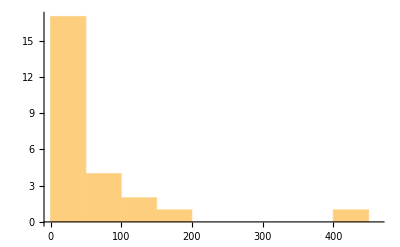

```mathematica
Histogram[Length/@actualSpecies]
```

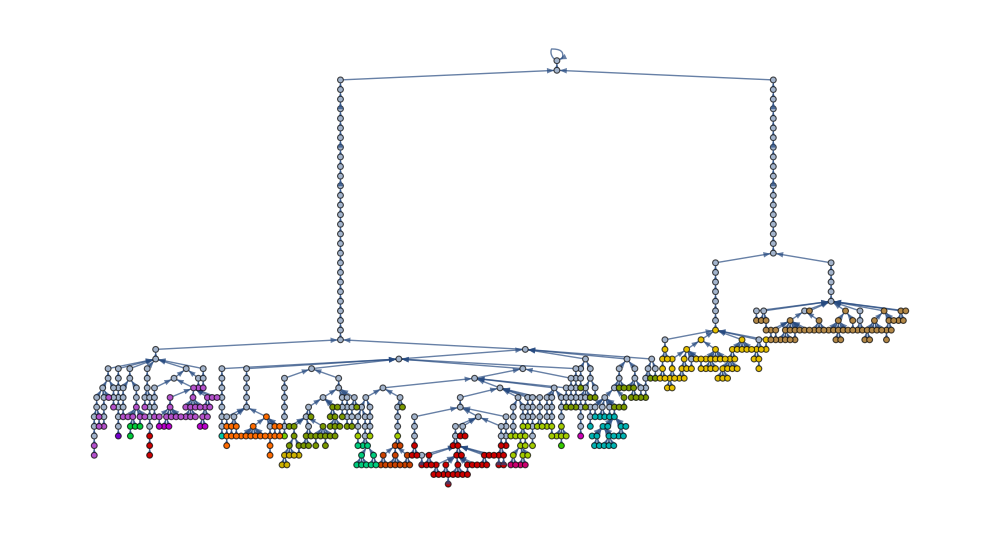

```mathematica
HighlightGraph[
Graph[EdgeList[g],
GraphLayout->{
"LayeredEmbedding",
"RootVertex"->Min[VertexList[g]],
"LeafDistance"->1/2
},
VertexLabels->Placed["Name",Tooltip]],
species,ImageSize->1000]
```